## Robot swarm with friction. Initial position is red rectangle.

```mathematica
DrawFrictionCor[A_,w_,L_,h_]:=
Module[{eps = 1/20,fs,rside,rtop,rbot, avey,vary,
mean1,avex1, varx1, cov1,cor1, 
mean2,avex2, varx2, cov2,cor2, 
mean3,avex3, varx3, cov3,cor3},
rside = Min[L+w,1];
rtop   = Min[A/w,If[L>1-w, 1-   h/L (1-w), 1-h]];
rbot   = Min[A/w,If[L>1-w,    h/L (1-w), h]];
avey = A/(2 w);
vary=A^2/(12 w^2);
avex1=(rbot w (L rbot+h w))/(2 A h);

mean1 = {avex1,avey};
varx1 = 1/(12 A^2 h^2)rbot w (-3 rbot w (L rbot+h w)^2+A (4 L^2 rbot^2+6 h L rbot w+4 h^2 w^2));
 cov1 = 1/(12 A h)rbot (-3 A (L rbot+h w)+rbot w (4 L rbot+3 h w));
cor1 = (rbot (-3 A (L rbot+h w)+rbot w (4 L rbot+3 h w)))/(A h √(A^2/w^2) √(1/(A^2 h^2)rbot w (-3 rbot w (L rbot+h w)^2+A (4 L^2 rbot^2+6 h L rbot w+4 h^2 w^2))));
avex2=1/(2 A h)w (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w));
varx2=1/(12 A^2 h^2)w (-3 w (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w))^2+2 A (2 L^2 rbot^3+3 h L rbot^2 w+2 h^2 (3 rbot rside (-rside+w)+rtop (3 rside^2-3 rside w+w^2))));
cov2=1/(12 A h)(-3 A (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w))+w (4 L rbot^3-3 h (2 rbot^2 (rside-w)+rtop^2 (-2 rside+w))));
cor2=(-3 A (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w))+w (4 L rbot^3-3 h (2 rbot^2 (rside-w)+rtop^2 (-2 rside+w))))/(A h √(A^2/w^2) √(1/(A^2 h^2)w (-3 w (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w))^2+2 A (2 L^2 rbot^3+3 h L rbot^2 w+2 h^2 (3 rbot rside (-rside+w)+rtop (3 rside^2-3 rside w+w^2))))));

mean2 = {avex2,avey};
avex3=1/(2 A h w)(-A^2 L+A w (2 h rside+2 L rtop-h w)+w^2 (L (rbot-rtop) (rbot+rtop)+2 h rbot (-rside+w)));
varx3=1/(12 A^2 h^2 w^2)(A^4 L^2+4 A (L^2 (rbot^3-3 rbot^2 rtop+2 rtop^3)-3 h L rbot (rbot-2 rtop) (rside-w)+3 h^2 rbot (rside-w)^2) w^3-3 w^4 (L (rbot-rtop) (rbot+rtop)+2 h rbot (-rside+w))^2+A^2 w^2 (6 L^2 (rbot-rtop) (rbot+rtop)+h^2 w^2+12 h L rbot (-rside+w)));
cov3=1/(12 A h w^2)(-A^3 L+3 A (L (-rbot^2+rtop^2)+2 h rbot (rside-w)) w^2+2 w^3 (L (2 rbot^3-rtop^3)+3 h rbot^2 (-rside+w)));
cor3=(A (-A^3 L+3 A (L (-rbot^2+rtop^2)+2 h rbot (rside-w)) w^2+2 w^3 (L (2 rbot^3-rtop^3)+3 h rbot^2 (-rside+w))))/(h (A^2/w^2)^(3/2) w^4 √(1/(A^2 h^2 w^2)(A^4 L^2+4 A (L^2 (rbot^3-3 rbot^2 rtop+2 rtop^3)-3 h L rbot (rbot-2 rtop) (rside-w)+3 h^2 rbot (rside-w)^2) w^3-3 w^4 (L (rbot-rtop) (rbot+rtop)+2 h rbot (-rside+w))^2+A^2 w^2 (6 L^2 (rbot-rtop) (rbot+rtop)+h^2 w^2+12 h L rbot (-rside+w)))));
mean3 = {avex3,avey};

If[w<A,w=A];
Graphics[{
(*Text[xyCorr[L,w,A,h],{0,.6}],*)
{Pink,Rectangle[{-eps,-eps},{1+eps,1+eps}],White,Rectangle[{0,0},{1,1}]},
(*draw friction zone*)
{Opacity[0.5],ChartElementData["GradientRectangle","ColorScheme"->"SiennaTones","GradientOrigin"->Bottom][{{0,1},{0,h}}],
ChartElementData["GradientRectangle","ColorScheme"->"SiennaTones","GradientOrigin"->Top][{{0,1},{1-h,1}}]},
(*draw Robots: possibly 3 sections*)
(*bottom parallelogon*)
{Blue,Polygon[{{0,0},{w,0},{w+L/h rbot,rbot},{L/h rbot,rbot}}]},
(*middle rectangle*)
If[rtop>rbot,{Blue,Polygon[{{rside,rbot},{rside,rtop},{rside-w,rtop},{rside-w,rbot}}]}],
(*top parallelogon*)
If[A/w>rtop,{Blue,Polygon[{{rside, rtop},{rside-L/h (A/w-rtop),A/w },{rside-w-L/h (A/w-rtop),A/w},{rside-w,rtop}}]}],
(*initial robot config*)
{EdgeForm[{Red}],FaceForm[],Rectangle[{0,0},{w,A/w}]},
{Red,Opacity[0.2],Rectangle[{0,0},{w,A/w}]},
(*initial robot config*)
{Dashed,Gray,Line[{{0,h},{1,h}}],Line[{{0,1-h},{1,1-h}}]},

(*centroids of individual parts*)
(*{Purple,PointSize[Large],Point[mean1]},
{Purple,PointSize[Large],Point[{ rside-w/2,(rbot+rtop)/2}]},
{Purple,PointSize[Large],Point[{ 1/2(rside-L/h (A/w-rtop)-w+rside),(A/w+rtop)/2}]},*)

(*draw the mean*) (*Point[If[A/w>rtop, {xave3,yave3}, If[rtop>rbot,{xave2,yave2},{xave1,yave1}]*)
{Red,PointSize[Large],Point[If[A/w>rtop,mean3, 
 If[rtop>rbot,mean2,
mean1]]]},
(*draw the covariance ellipse*)
{ColorData[97,"ColorList"]⟦3⟧,Opacity[0],EdgeForm[{Thick,Red}],
If[A/w>rtop,Ellipsoid[mean3,4{{varx3, cov3},{cov3,vary}}], 
 If[rtop>rbot,Ellipsoid[mean2,4{{varx2, cov2},{cov2,vary}}],
Ellipsoid[mean1,4{{varx1, cov1},{cov1,vary}}]]]
},
fs = 16;
Text[Style[StringForm["SubscriptBox[\"ρ\", 
 StyleBox[\"xy\",\nFontSlant->\"Italic\"]]=``",
Round[If[A/w>rtop,cor3 ,
 If[rtop>rbot,cor2,cor1]
],0.01]],Directive[FontFamily->"Times",FontSize->fs]],{1/2,1.32}],
Text[Style[StringForm["
StyleBox[\"A\",\nFontSlant->\"Italic\"]=``,",  (*Mistral*)
Round[A,0.01]],Directive[FontFamily->"Times",FontSize->fs]],{.3,1.21}],
Text[Style[StringForm["l" (*Mistral*)],Directive[FontFamily->"Mistral",FontSize->fs]],{.55,1.21}],
Text[Style[StringForm[" =``",  (*Mistral*)
Round[h,0.01]],Directive[FontFamily->"Times",FontSize->fs]],{.7,1.21}],
Text[Style[StringForm["
StyleBox[\"w\",\nFontSlant->\"Italic\"]=``, 
StyleBox[\"L\",\nFontSlant->\"Italic\"]=``",
Round[w,0.01],Round[L,0.01]],Directive[FontFamily->"Times",FontSize->fs]],{1/2,1.1}]

},ImageSize->430,PlotRange->{{-1,2},{-.1,1.4}}]]
Manipulate[(*controls: A, w, h, L*)
DrawFrictionCor[A,w,L,h],
{{A,1/8},0.001,1,Appearance->"Labeled"},
{{w,1/4},0.001,1,Appearance->"Labeled"},
{{h,1/4},0.0001,1/2 (*only stretch half the workspace*),Appearance->"Labeled"},
{L,0,2(*we could make this bigger*),Appearance->"Labeled"}
]
```

{0.770165,{L→0.623975,w→0.376025}}

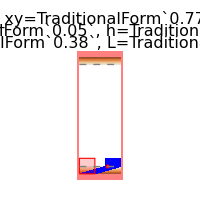

```mathematica
A=0.05;h = 1/16;
 s = NMaximize[{corcalc[A,L,h,w],w≥ A,w≤ 1,L≥0},{L,w}]
DrawFrictionCor[A,s⟦2,2,2⟧,s⟦2,1,2⟧,h]
```

{0.979033,{L→0.826093,w→0.173907}}

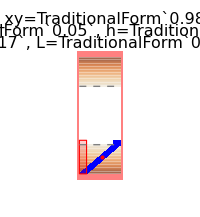

```mathematica
A=0.05;h = 1/4;
 s = NMaximize[{corcalc[A,L,h,w],w≥ A,w≤ 1,L≥0},{L,w}]
DrawFrictionCor[A,s⟦2,2,2⟧,s⟦2,1,2⟧,h]
```

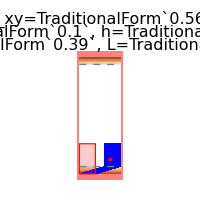

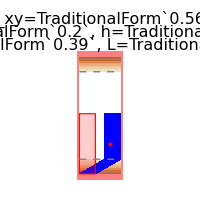

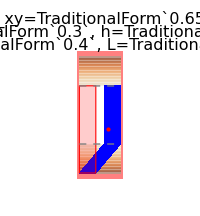

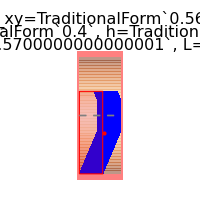

```mathematica
A=0.1;h = 1/16;
 s = NMaximize[{corcalc[A,L,h,w],w≥ A,w≤ 1,L≥0},{L,w}];
DrawFrictionCor[A,s⟦2,2,2⟧,s⟦2,1,2⟧,h]
A=0.2;h = 1/8;
 s = NMaximize[{corcalc[A,L,h,w],w≥ A,w≤ 1,L≥0},{L,w}];
DrawFrictionCor[A,s⟦2,2,2⟧,s⟦2,1,2⟧,h]
A=0.3;h = 1/4;
 s = NMaximize[{corcalc[A,L,h,w],w≥ A,w≤ 1,L≥0},{L,w}];
DrawFrictionCor[A,s⟦2,2,2⟧,s⟦2,1,2⟧,h]
A=0.4;h = 1/2;
 s = NMaximize[{corcalc[A,L,h,w],w≥ A,w≤ 1,L≥0},{L,w}];
DrawFrictionCor[A,s⟦2,2,2⟧,s⟦2,1,2⟧,h]
```

## Correlation as a function of Area of the robot swarm under gravity input. assume robot swarm of total area A. Maximum correlation of the swarm occurs when it is pushed input a corner and makes a 45-45-90 triangle (correlation is 1/2) -Graphics-

```mathematica
Corxy[β_,A_]:=Which[A≤1/2,Piecewise[{{-(Tan[β] √(12 A^2-Tan[β]^2))/(√(48 A^4+24 A^2 Tan[β]^2-Tan[β]^4)), (0≤ β≤ ArcTan[2 A]) || (2 π - ArcTan[2 A] < β ≤  2π)}, {-1/2, ArcTan[2A]<β≤ π/2-ArcTan[2A]}, {-(Cot[β] √(12 A^2-Cot[β]^2))/(√(48 A^4+24 A^2 Cot[β]^2-Cot[β]^4)), π/2-ArcTan[2A]<β≤π/2+ArcTan[2A]}, {1/2, π/2+ArcTan[2A]< β≤ π-ArcTan[2A]}, {-(Tan[β] √(12 A^2-Tan[β]^2))/(√(48 A^4+24 A^2 Tan[β]^2-Tan[β]^4)), π-ArcTan[2 A]<β≤π+ArcTan[2 A]}, {-1/2, π+ArcTan[2A]< β≤ (3π)/2-ArcTan[2A]}, {-(Cot[β] √(12 A^2-Cot[β]^2))/(√(48 A^4+24 A^2 Cot[β]^2-Cot[β]^4)), (3π)/2-ArcTan[2A]<β≤(3π)/2+ArcTan[2A]}, {1/2, (3π)/2+ArcTan[2A]< β≤ 2π-ArcTan[2A]}}],
1/2<A<1,
Piecewise[{{-(Tan[β] √(12 A^2-Tan[β]^2))/(√(48 A^4+24 A^2 Tan[β]^2-Tan[β]^4)), (0≤ β≤ ArcTan[1/2,(1-A)]) || (2 π - ArcTan[1/2,(1-A)] < β ≤  2π)}, {((-1+A) (17+2 (-5+A) A-6 √2 (√((1-A) Cot[β])+ √((1-A)  Tan[β]))))/(√(-4 (-1+A)^2 (2+A) Cot[β]+3 (-3+4A+(1-A)4 √2 √((1-A)  Cot[β]))) √(-4 (-1+A)^2 (2+A) Tan[β]+3 (-3+4A+(1-A)4 √2 √((1-A)  Tan[β])))), ArcTan[1/2,(1-A)]< β≤ π/2-ArcTan[1/2,1-A]}, {-(Cot[β] √(12 A^2-Cot[β]^2))/(√(48 A^4+24 A^2 Cot[β]^2-Cot[β]^4)), π/2-ArcTan[1/2,1-A]<β≤ π/2+ArcTan[1/2,1-A]}, {-((-1+A) (17+2 (-5+A) A-6 √2 √((A-1) Cot[β])-6 √2 √((A-1) Tan[β])))/(√(4 (-1+A)^2 (2+A) Cot[β]+3 (-3+4A +4 (1-A)√2 √((A-1) Cot[β]))) √(4 (-1+A)^2 (2+A) Tan[β]+3 (-3+4A+(1-A)4 √2 √((A-1)Tan[β])))), π/2+ArcTan[1/2,1-A]< β≤ π-ArcTan[1/2,1-A]}, {-(Tan[β] √(12 A^2-Tan[β]^2))/(√(48 A^4+24 A^2 Tan[β]^2-Tan[β]^4)), π-ArcTan[1/2,1- A]<β≤ π+ArcTan[1/2,1- A]}, {((-1+A) (17+2 (-5+A) A-6 √2 (√((1-A) Cot[β])+ √((1-A)  Tan[β]))))/(√(-4 (-1+A)^2 (2+A) Cot[β]+3 (-3+4A+(1-A)4 √2 √((1-A)  Cot[β]))) √(-4 (-1+A)^2 (2+A) Tan[β]+3 (-3+4A+(1-A)4 √2 √((1-A)  Tan[β])))), π+ArcTan[1/2,1-A]< β≤ (3π)/2-ArcTan[1/2,1-A]}, {-(Cot[β] √(12 A^2-Cot[β]^2))/(√(48 A^4+24 A^2 Cot[β]^2-Cot[β]^4)), (3π)/2-ArcTan[1/2,1-A]<β≤ (3π)/2+ArcTan[1/2,1-A]}, {-((-1+A) (17+2 (-5+A) A-6 √2 √((A-1) Cot[β])-6 √2 √((A-1) Tan[β])))/(√(4 (-1+A)^2 (2+A) Cot[β]+3 (-3+4A +4 (1-A)√2 √((A-1) Cot[β]))) √(4 (-1+A)^2 (2+A) Tan[β]+3 (-3+4A+(1-A)4 √2 √((A-1)Tan[β])))), (3π)/2+ArcTan[1/2,1-A]< β≤2 π - ArcTan[1/2,(1-A)]}}],
A==1,0]
```

```mathematica
Assuming[A≥ 0 && A≤1,FullSimplify[Corxy[3π/4,A]]]
```

Piecewise[{{1/2, 2 A≤1&&4 ArcTan[2 A]<π}, {((-1+A) (17-12 √(2-2 A)+2 (-5+A) A))/(17-12 √(2-2 A)+4 A (-6+3 √(2-2 A)+A^2)), 1/2<A<1&&4 ArcTan[2-2 A]<π}, {√((-1+12 A^2)/(-1+24 A^2+48 A^4)), (1/2<A<1&&4 ArcTan[2-2 A]≥π)||(2 A≤1&&4 ArcTan[2 A]≥π)}, {0, True}}]

```mathematica
Assuming[A>1/2 && A<1,[((-1+A) (17-12 √(2-2 A)+2 (-5+A) A))/(17-12 √(2-2 A)+4 A (-6+3 √(2-2 A)+A^2))]]
```

```mathematica
((A-1) (17-12 √2 √(1-A)-10 A+2 A^2))/(17-12 √2 √(1-A)-24 A+12 √2 √(1-A) A+4 A^3)
((A-1) (17-12 √2 √(1-A)-10 A+2 A^2))/(17+√2 √(1-A)(12A-12)-24 A+4 A^3)
```

```mathematica
Expand[(A-1) (17-12 √2 √(1-A)-10 A+2 A^2)]
Expand[17-12 √(2-2 A)+4 A (-6+3 √(2-2 A)+A^2)]
```

```mathematica
-17+12 √(2-2 A)+27 A-12 √(2-2 A) A-12 A^2+2 A^3
```

17-12 √(2-2 A)-24 A+12 √(2-2 A) A+4 A^3

```mathematica
-(17-12 √(2-2 A)-24 A-3 A+12 √(2-2 A) A+12 A^2+4 A^3-6 A^3)/(17-12 √(2-2 A)-24 A+12 √(2-2 A) A+4 A^3)
-(17-12 √(2-2 A)-24 A+12 √(2-2 A) A+4 A^3+12 A^2-3 A-6 A^3)/(17-12 √(2-2 A)-24 A+12 √(2-2 A) A+4 A^3)
-1-(-3 A+12 A^2-6 A^3)/(17-12 √(2-2 A)-24 A+12 √(2-2 A) A+4 A^3)
-1+3A(1-4 A+2 A^2)/(17-12 √(2-2 A)-24 A+12 √(2-2 A) A+4 A^3)
```

```mathematica
FullSimplify[-1+3A(1-4 A+2 A^2)/(17-12 √(2-2 A)-24 A+12 √(2-2 A) A+4 A^3)]
```

-1+(3 A (1+2 (-2+A) A))/(17-12 √(2-2 A)+4 A (-6+3 √(2-2 A)+A^2))

```mathematica
-1+(3 A (1+2 (-2+A) A))/(17+√2 √(1-A)(12A-12)-24 A+4 A^3)
```

```mathematica
Plot[{Corxy[3π/4,A],If[A<1/2,1/2,-1+(3 A (1+2 (-2+A) A))/(17-12 √(2-2 A)+4 A (-6+3 √(2-2 A)+A^2))]} ,{A,0,1},PlotLegends->Placed[{"Gravity","Friction"},{Bottom,Center}],AxesLabel->{"A","Corr"}]
```

-Graphics-

## Correlation as a function of Area of the robot swarm using wall friction. assume robot swarm of total area A is initialized in a rectangle w wide by A/wtall in the lower left corner of a square workspace with sides of lenght 1. If the swarm is pushed to the right a distance L∈[0,1-w], and the boundary layer height is h, what is the maximum correlation?

### The y mean and y-variance are unchanged by a dragging motion

```mathematica
yave = FullSimplify[Simplify[(∫_0^(A/w) y w ⅆy)/A]] (*y-mean never changes = A/(2 w)*)
yvar = FullSimplify[Simplify[(∫_0^(A/w) y^2 w ⅆy)/A]-(A/(2 w))^2] (*y-variance never changes = A^2/(12 w^2)*)
```

A/(2 w)

A^2/(12 w^2)

### Compute Values if swarm is entirely in the lower linear friction boundry layer. Assuming A/w<h,

```mathematica
xave1 = FullSimplify[(*lower parallelogram*)(∫_0^rbot (∫_(L/h y)^(L/h y+w) xⅆx)ⅆy)/A]
xvar1= FullSimplify[Simplify[(∫_0^rbot (∫_(L/h y)^(w+L/h y) x^2 ⅆx)ⅆy)/A]-xave1^2]
covxy1 = FullSimplify[Simplify[(*lower parallelogram*)(∫_0^rbot (∫_(L/h y)^(w+L/h y) x*yⅆx)ⅆy)/A]-xave1*yave]
corxy1=FullSimplify[covxy1/(Sqrt[xvar1]*Sqrt[yvar])]
```

(rbot w (L rbot+h w))/(2 A h)

(rbot w (-3 rbot w (L rbot+h w)^2+A (4 L^2 rbot^2+6 h L rbot w+4 h^2 w^2)))/(12 A^2 h^2)

(rbot (-3 A (L rbot+h w)+rbot w (4 L rbot+3 h w)))/(12 A h)

(rbot (-3 A (L rbot+h w)+rbot w (4 L rbot+3 h w)))/(A h √(A^2/w^2) √((rbot w (-3 rbot w (L rbot+h w)^2+A (4 L^2 rbot^2+6 h L rbot w+4 h^2 w^2)))/(A^2 h^2)))

### Compute Values if swarm is entirely below the upper friction boundry layer (A/w < 1-h).

```mathematica
xave2 = FullSimplify[(*lower parallelogram*)(∫_0^rbot (∫_(L/h y)^(L/h y+w) xⅆx)ⅆy+∫_rbot^rtop (∫_(rside-w)^rside xⅆx)ⅆy)/A]
xvar2= FullSimplify[Simplify[(∫_0^rbot (∫_(L/h y)^(w+L/h y) x^2 ⅆx)ⅆy+∫_rbot^rtop (∫_(rside-w)^rside x^2 ⅆx)ⅆy)/A]-xave2^2]
covxy2 = FullSimplify[Simplify[(*lower parallelogram*)(∫_0^rbot (∫_(L/h y)^(w+L/h y) x*yⅆx)ⅆy+∫_rbot^rtop (∫_(rside-w)^rside x* yⅆx)ⅆy)/A]-xave2*yave]
corxy2=FullSimplify[covxy2/(Sqrt[xvar2]*Sqrt[yvar])]
```

```mathematica
xave2=(w (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w)))/(2 A h);
xvar2=1/(12 A^2 h^2)w ;(-3 w (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w))^2+2 A (2 L^2 rbot^3+3 h L rbot^2 w+2 h^2 (3 rbot rside (-rside+w)+rtop (3 rside^2-3 rside w+w^2))))
covxy2=1/(12 A h)(-3 A (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w))+w (4 L rbot^3-3 h (2 rbot^2 (rside-w)+rtop^2 (-2 rside+w))));
corxy2=(-3 A (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w))+w (4 L rbot^3-3 h (2 rbot^2 (rside-w)+rtop^2 (-2 rside+w))))/(A h √(A^2/w^2) √(1/(A^2 h^2)w (-3 w (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w))^2+2 A (2 L^2 rbot^3+3 h L rbot^2 w+2 h^2 (3 rbot rside (-rside+w)+rtop (3 rside^2-3 rside w+w^2))))));
```

### Compute Values if swarm is extend into the upper friction boundry layer (A/w > 1-h).

```mathematica
xave3 = FullSimplify[(*lower parallelogram*)(∫_0^rbot (∫_(L/h y)^(L/h y+w) xⅆx)ⅆy+∫_rbot^rtop (∫_(rside-w)^rside xⅆx)ⅆy+∫_rtop^(A/w) (∫_(rside-L/h (y-rtop)-w)^(rside-L/h (y-rtop)) xⅆx)ⅆy)/A]
xvar3= FullSimplify[Simplify[(∫_0^rbot (∫_(L/h y)^(w+L/h y) x^2 ⅆx)ⅆy+∫_rbot^rtop (∫_(rside-w)^rside x^2 ⅆx)ⅆy+∫_rtop^(A/w) (∫_(rside-L/h (y-rtop)-w)^(rside-L/h (y-rtop)) x^2 ⅆx)ⅆy)/A]-xave3^2]
covxy3 = FullSimplify[Simplify[(*lower parallelogram*)(∫_0^rbot (∫_(L/h y)^(w+L/h y) x*yⅆx)ⅆy+∫_rbot^rtop (∫_(rside-w)^rside x* yⅆx)ⅆy+∫_rtop^(A/w) (∫_(rside-L/h (y-rtop)-w)^(rside-L/h (y-rtop)) x*yⅆx)ⅆy)/A]-xave3*yave]
corxy3=FullSimplify[covxy3/(Sqrt[xvar3]*Sqrt[yvar])]
```

### Parameterized versions of correlation

```mathematica
corcalc[A_,L_,h_,w_]:=Module[{rtop ,rside ,rbot},
rtop   = Min[A/w,If[L>1-w, 1-   h/L (1-w), 1-h]];
rside = Min[L+w,1];
rbot   = Min[A/w,If[L>1-w,    h/L (1-w), h]];
If[A/w>rtop,(A (-A^3 L+3 A (L (-rbot^2+rtop^2)+2 h rbot (rside-w)) w^2+2 w^3 (L (2 rbot^3-rtop^3)+3 h rbot^2 (-rside+w))))/(h (A^2/w^2)^(3/2) w^4 √(1/(A^2 h^2 w^2)(A^4 L^2+4 A (L^2 (rbot^3-3 rbot^2 rtop+2 rtop^3)-3 h L rbot (rbot-2 rtop) (rside-w)+3 h^2 rbot (rside-w)^2) w^3-3 w^4 (L (rbot-rtop) (rbot+rtop)+2 h rbot (-rside+w))^2+A^2 w^2 (6 L^2 (rbot-rtop) (rbot+rtop)+h^2 w^2+12 h L rbot (-rside+w))))), 
 If[rtop>rbot,(-3 A (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w))+w (4 L rbot^3-3 h (2 rbot^2 (rside-w)+rtop^2 (-2 rside+w))))/(A h √(A^2/w^2) √(1/(A^2 h^2)w (-3 w (L rbot^2+h (-2 rbot rside+2 rside rtop+2 rbot w-rtop w))^2+2 A (2 L^2 rbot^3+3 h L rbot^2 w+2 h^2 (3 rbot rside (-rside+w)+rtop (3 rside^2-3 rside w+w^2)))))),
(rbot (-3 A (L rbot+h w)+rbot w (4 L rbot+3 h w)))/(A h √(A^2/w^2) √((rbot w (-3 rbot w (L rbot+h w)^2+A (4 L^2 rbot^2+6 h L rbot w+4 h^2 w^2)))/(A^2 h^2)))]]]
```

### Parameterized versions of correlation

```mathematica
gcorr=Plot[Corxy[3π/4,A],{A,0,1},PlotLegends->Placed[{"Stable Config.","Friction"},{Bottom,Center}],AxesLabel->{"A","Corr"},PlotStyle->ColorData[97,5]]
```

-Graphics-

```mathematica
Clear[As]
NArgMax[{corcalc[As,L,1/2,w],w≥ As,w≤ 1,L≥0,As≥ 0,As≤ 1},{As,w,L}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

NArgMax::nnum: The function value Indeterminate is not a number at {As, L, w} = {0., 9.59105, -4.36321×10^-6}.

{5.66097×10^-7,9.54749,-3.21821×10^-6}

```mathematica
Position[Abs[tblHp50⟦;;,2⟧-.5],_?(#==Min[Abs[tblHp50⟦;;,2⟧-.5]]&)]
```

{{44}}

```mathematica
tblHp50⟦44⟧
```

{0.431,0.50397,0.579721,0.594052}

```mathematica
tblHp50⟦;;,2⟧
```

{0.999998,0.999753,0.999082,0.997963,0.996371,0.994283,0.991677,0.98853,0.984821,0.980528,0.975634,0.970119,0.963969,0.95717,0.949711,0.941584,0.932782,0.923305,0.913152,0.902329,0.890842,0.878703,0.865926,0.85253,0.838536,0.823968,0.808855,0.793225,0.777111,0.76055,0.743576,0.726229,0.708549,0.690577,0.672355,0.653924,0.635327,0.616606,0.597803,0.57896,0.560117,0.541313,0.522585,0.50397,0.485503,0.467216,0.449139,0.431301,0.413729,0.396446,0.379475,0.362835,0.346543,0.330614,0.315063,0.299899,0.285133,0.270772,0.256821,0.243285,0.230166,0.217466,0.205184,0.193321,0.181873,0.170839,0.160214,0.149994,0.140174,0.130749,0.121713,0.11306,0.104783,0.0968757,0.0893312,0.0821427,0.0753032,0.0688056,0.062643,0.0568086,0.0512954,0.0460968,0.0412063,0.0366175,0.0323243,0.0283206,0.0246009,0.0211596,0.0179915,0.0150919,0.0124563,0.0100804,0.00796055,0.00609359,0.0044768,0.00310818,0.00198655,0.00111186,0.000485637,0.000112039}

```mathematica
tblHp50=Table[s = NMaximize[{corcalc[As,L,1/2,w],w≥ As,w≤ 1,L≥0},{L,w}];
{As,s⟦1⟧,s⟦2,1,2⟧,s⟦2,2,2⟧}, {As,0.001,1,.01}];
tblHp25=Table[s = NMaximize[{corcalc[As,L,1/4,w],w≥ As,w≤ 1,L≥0},{L,w}];
{As,s⟦1⟧,s⟦2,1,2⟧,s⟦2,2,2⟧}, {As,0.001,1,.01}];
tblHp125=Table[s = NMaximize[{corcalc[As,L,1/8,w],w≥ As,w≤ 1,L≥0},{L,w}];
{As,s⟦1⟧,s⟦2,1,2⟧,s⟦2,2,2⟧}, {As,0.001,1,.01}];
tblHp0625=Table[s = NMaximize[{corcalc[As,L,1/16,w],w≥ As,w≤ 1,L≥0},{L,w}];
{As,s⟦1⟧,s⟦2,1,2⟧,s⟦2,2,2⟧}, {As,0.001,1,.01}];
```

```mathematica
corrF =ListPlot[{
Transpose[{tblHp50⟦;;,1⟧,tblHp50⟦;;,2⟧}],
Transpose[{tblHp25⟦;;,1⟧,tblHp25⟦;;,2⟧}],
Transpose[{tblHp125⟦;;,1⟧,tblHp125⟦;;,2⟧}],
Transpose[{tblHp0625⟦;;,1⟧,tblHp0625⟦;;,2⟧}]
},AspectRatio->1/3,Joined->True,InterpolationOrder->2, 
LabelStyle->Black,
TicksStyle->Directive[Black],PlotLegends->Placed[{"F, h=1/2","F, h=1/4","F, h=1/8","F, h=1/16"},{Bottom,Center}],AxesLabel->{"A","ρ_xy"}]
```

-Graphics-

```mathematica
corrBestL =ListPlot[{
Transpose[{tblHp50⟦;;,1⟧,tblHp50⟦;;,3⟧}],
Transpose[{tblHp25⟦;;,1⟧,tblHp25⟦;;,3⟧}],
Transpose[{tblHp125⟦;;,1⟧,tblHp125⟦;;,3⟧}]
},Joined->True,InterpolationOrder->2, PlotLegends->Placed[{"F,h=1/2","F,h=1/4","F,h=1/8"},{Bottom,Center}],AxesLabel->{"A","L"}]
```

-Graphics-

```mathematica
corrBestw =ListPlot[{
Transpose[{tblHp50⟦;;,1⟧,tblHp50⟦;;,4⟧}],
Transpose[{tblHp25⟦;;,1⟧,tblHp25⟦;;,4⟧}],
Transpose[{tblHp125⟦;;,1⟧,tblHp125⟦;;,4⟧}]
},Joined->True,InterpolationOrder->2, PlotLegends->Placed[{"F,h=1/2","F, h=1/4","F, h=1/8","F, h=1/16"},{Bottom,Center}],AxesLabel->{"A","w"}]
```

-Graphics-

```mathematica
Show[{corrF,gcorr}]
```

-Graphics-

```mathematica
hs = 1/2;As = 3/4;
Maximize[{corcalc[As,L,hs,w],w≥ As,w≤ 1,L≥0},{L,w}]
```

$Aborted

```mathematica
hs = 1/2;As = 3/4;
Plot3D[corcalc[As,L,hs,w],{L,0,3},{w,As,1},AxesLabel->{"L","w"},PlotLabel->StringForm["Friction boundary layer ``, Area = ``",hs,As] ,PlotRange->{Automatic,{0,1}}]
```

-Graphics3D-

```mathematica
hs = 1/4;As = 1/16;
Plot3D[corcalc[As,L,hs,w],{L,0,3},{w,As,1},AxesLabel->{"L","w"},PlotLabel->StringForm["Friction boundary layer ``, Area = ``",hs,As] ,PlotRange->{Automatic,{0,1}}]
```

## Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null